# Comms final project: Acoustic Modem

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## Shared constants

```mathematica
Global`databaud = Quantity[40, "Hertz"];(* hertz *)
Global`speakerbaud = Quantity[40000, "Hertz"];(* hertz *)
Global`carrierfreq=Quantity[400, "Hertz"];(* hertz *)
```

```mathematica
symbolBases=Exp[# I]&/@{0,Pi}
```

{1,-1}

The start of the signal is denoted by a chirp

```mathematica
SeedRandom["notallthatrandom"]
Global`signalStart=RandomReal[{-1,1},speakerbaud/databaud*3];

SeedRandom[]
```

## Transmitter

```mathematica
With[{context="tx`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Step 1: Generate signal codes

```mathematica
codeLen=speakerbaud/databaud;
```

The codes are still complex at this point, and will only be transformed to real space before being played.

```mathematica
baseCode = Exp[I 2Pi QuantityMagnitude@carrierfreq #]&/@N@Range[0,1/QuantityMagnitude@databaud,1/QuantityMagnitude@speakerbaud][[;;-2]];
codes=baseCode*#&/@symbolBases;
```

### Step 2: Retrieve data to transmit

```mathematica
rawdata="does this thing work?";
```

### Step 3: Convert data to symbols

```mathematica
bytes=ToCharacterCode@rawdata
symbols=Flatten[IntegerDigits[#,2,8]&/@bytes];
symbols
```

{100,111,101,115,32,116,104,105,115,32,116,104,105,110,103,32,119,111,114,107,63}

{0,1,1,0,0,1,0,0,0,1,1,0,1,1,1,1,0,1,1,0,0,1,0,1,0,1,1,1,0,0,1,1,0,0,1,0,0,0,0,0,0,1,1,1,0,1,0,0,0,1,1,0,1,0,0,0,0,1,1,0,1,0,0,1,0,1,1,1,0,0,1,1,0,0,1,0,0,0,0,0,0,1,1,1,0,1,0,0,0,1,1,0,1,0,0,0,0,1,1,0,1,0,0,1,0,1,1,0,1,1,1,0,0,1,1,0,0,1,1,1,0,0,1,0,0,0,0,0,0,1,1,1,0,1,1,1,0,1,1,0,1,1,1,1,0,1,1,1,0,0,1,0,0,1,1,0,1,0,1,1,0,0,1,1,1,1,1,1}

### Step 4: Interleave transmit codes

```mathematica
signal=Flatten[codes[[#+1]]&/@symbols];
```

### Step 4.5: Prepend start code

```mathematica
signal=Join[signalStart,signal];
```

```mathematica
startDelay=RandomInteger[10000]
signal=Join[ConstantArray[0,startDelay],signal];
```

9612

### Step 5: Transmit and save

```mathematica
sound=SampledSoundList[Re@signal,QuantityMagnitude@speakerbaud];
```

```mathematica
EmitSound[sound]
```

```mathematica
Export["test data\output.wav",sound]
```

test data\output.wav

### Cleanup

```mathematica
With[{context="tx`"},If[Context[]==context,End[],"Not in context"]]
```

tx`

## Record a sound

```mathematica
recorded=SystemDialogInput["RecordSound"];
```

```mathematica
Head@recorded
```

Sound

```mathematica
resampled=AudioResample[recorded,QuantityMagnitude@speakerbaud];
```

```mathematica
inputSound=AudioData[resampled];
If[Depth[inputSound]>2,inputSound=inputSound[[1]];]
```

## Receiver

```mathematica
With[{context="rx`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

### Read in the audio data

```mathematica
inputSound=Import["test data/output.wav","Data"];
```

### Find the agreed-upon start code, then crop to it

TODO: do this

```mathematica
conv=ListCorrelate[signalStart,inputSound];
```

```mathematica
matchpoint=Ordering[conv,-1][[1]]
```

149408

```mathematica
croppedsound=inputSound[[matchpoint+Length@signalStart;;]];
```

```mathematica
ListLinePlot[conv,PlotRange->Full]
```

-Graphics-

### Chop the sound into databaud long segments

```mathematica
segments=Partition[croppedsound,speakerbaud/databaud];
Dimensions@segments
```

{219,1000}

### For each segment, identify the most likely symbol

```mathematica
baseCode = Exp[I 2Pi QuantityMagnitude@carrierfreq #]&/@N@Range[0,1/QuantityMagnitude@databaud,1/QuantityMagnitude@speakerbaud][[;;-2]];
Length@baseCode
```

1000

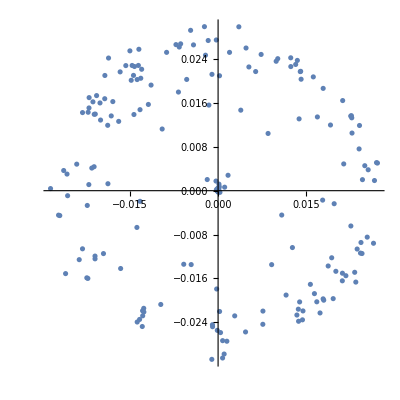

```mathematica
ratios=2/(Length@baseCode)Dot[baseCode,#]&/@segments;
ListPlot[(Tooltip[{Re[#1],Im[#1]},#1]&)/@ratios,AspectRatio->1]
```

TODO: Correct for drift in phase space with clever snapping algorithms.

```mathematica
bestSymbol[ratio_]:=
Module[{differences},
differences=Abs[ratio-symbolBases];
Ordering[differences,1][[1]]-1
]
```

```mathematica
symbols=bestSymbol/@ratios
```

{0,1,1,0,0,1,0,0,0,1,1,0,1,1,1,1,0,1,1,0,0,1,0,1,0,1,1,1,0,0,1,1,0,0,1,0,0,0,0,0,1,1,0,0,1,1,1,1,1,0,0,1,0,1,1,1,1,0,0,1,0,1,1,0,1,0,0,0,1,1,0,0,1,1,0,1,1,1,1,1,0,0,1,1,0,1,0,0,0,1,1,0,1,0,0,0,0,1,1,0,1,0,1,1,0,0,0,1,0,0,0,1,1,0,0,1,1,0,0,0,1,1,0,1,0,0,0,0,0,1,1,1,0,1,1,1,0,1,0,1,1,0,0,0,1,0,0,0,1,1,0,1,1,0,1,0,1,0,1,1,0,0,1,1,1,1,1,0,1,1,0,0,1,0,1,1,0,1,1,1,1,1,1,0,0,0,0,1,1,1,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,0,1,1,0,0,0,0,0,0,0,0,1}

### Convert the symbols back into text

```mathematica
bytes=FromDigits[#,2]&/@Partition[symbols,8]
```

{100,111,101,115,32,207,151,150,140,223,52,104,107,17,152,208,119,88,141,171,62,203,126,29,214,116,192}

```mathematica
output=FromCharacterCode@bytes
```

does Ï.97.96.8cß4hk.11.98ÐwX.8d«>Ë~.1dÖtÀ

### Cleanup

```mathematica
With[{context="rx`"},If[Context[]==context,End[],"Not in context"]]
```

rx`